```mathematica
SetDirectory["C:\\Users\\ulano\\source\\repos\\masz"]
```

C:\Users\ulano\source\repos\masz

Character Interaction Networks for George R. R. Martin’s “A Song of Ice and Fire” saga

```mathematica
dataset1 =Drop[Import["asoiaf.csv"],1];
```

```mathematica
edges1 =Map[#1[[1]]->#1[[2]]&,dataset1];
```

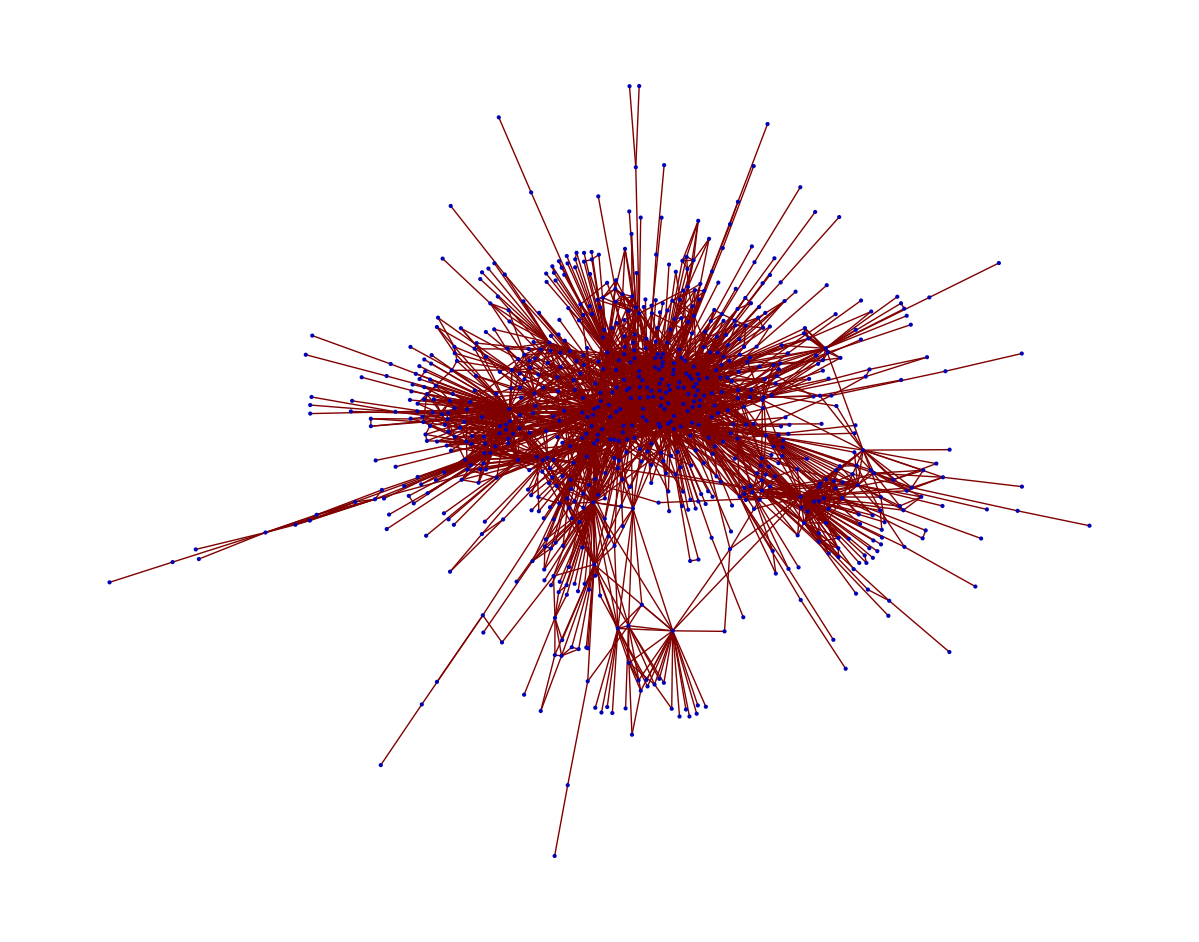

```mathematica
GraphPlot[edges1]
```

```mathematica
dataset2 =Drop[Import["s1gotEdges.csv"],1];
```

```mathematica
edges2 =Map[#1[[1]]->#1[[2]]&,dataset2];
```

```mathematica
GraphPlot3D[edges2,Boxed->False,VertexLabeling->False,VertexRenderingFunction->({Sphere[#,0.05],Black}&)]
```

-Graphics3D-

Real-world animal interaction network data sets. Animal interaction data from published studies of wild, captive, and domesticated animals.

```mathematica
dataset3 =Import["aves-barn-swallow-contact-network.csv"];
g3 =Graph[Map[#1[[1]]->#1[[2]]&,dataset3]];
vd=Thread[VertexList@g3->10*Normalize[VertexDegree@g3,Total]];
g3out=SetProperty[g3,VertexSize->vd]
```

-Graphics-

Visualize road-euroroad’s link structure and discover valuable insights using the interactive network data visualization and analytics platform. Compare with hundreds of other network data sets across many different categories and domains.

```mathematica
dataset4 =Import["road-euroroad.csv"];
edges4=Map[#1[[1]]->#1[[2]]&,dataset4];
HighlightGraph[Graph[edges4],%]
```

-Graphics-

Visualize cit-DBLP’s link structure and discover valuable insights using the interactive network data visualization and analytics platform. Compare with hundreds of other network data sets across many different categories and domains.

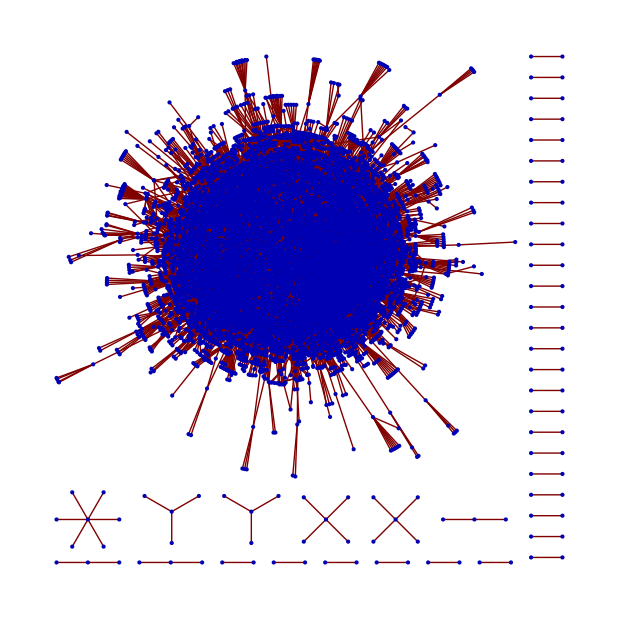

```mathematica
dataset5 =Import["cit-DBLP.csv"];
edges5=Map[#1[[1]]->#1[[2]]&,dataset5];
GraphPlot[Graph[edges5]]
```

Songbirds

```mathematica
dataset6 =Import["aves-songbird-social.csv"];
edges6=Map[#1[[1]]->#1[[2]]&,dataset6];
CommunityGraphPlot[Graph[edges6]]
```

-Graphics-

Human Contact Network

```mathematica
dataset7 =Import["infect-hyper.csv"];
edges7=Map[#1[[1]]->#1[[2]]&,dataset7];
CommunityGraphPlot[Graph[edges7]]
```

-Graphics-

Visualize ENZYMES-g285’s link structure and discover valuable insights using our

```mathematica
dataset8 =Import["enzymes.csv"];
edges8=Map[#1[[1]]->#1[[2]]&,dataset8];
g8= Graph[edges8];
GraphHub[g8];
HighlightGraph[g8,%,VertexSize->1]
```

-Graphics-